```mathematica
(*longks={{0,0},{1,0},{0,1},{2,0},{1,1},{0,2},{3,0},{2,1},{1,2},{0,3},{4,0},{3,1},{2,2},{1,3},{0,4},{5,0},{4,1},{3,2},{2,3},{1,4},{0,5},{6,0},{5,1},{4,2},{3,3},{2,4},{1,5},{0,6},{7,0},{6,1},{5,2},{4,3},{3,4},{2,5},{1,6},{0,7},{7,1},{6,2},{5,3},{3,5},{2,6},{1,7},{7,2},{6,3},{3,6},{2,7},{7,3},{3,7}};
<<ToMatlab`
Table[SetPrecision[momRRd[longks[[i,1]],longks[[i,2]]],40],{i,1,Length[longks]}]//ToMatlab;*)
```

```mathematica
ClearAll["Global`*"];
(* Upper limit: 
{X, 1, 0.25, 0.101, 0.0211, 0.00625} 
*)
(*rmins={10^-6,10^-6,0.001,0.1,0.1,0.1,0.1};*)
(*rminsR=10^-12{1,1,1,1};*)
rminsR={10^-16,10^-10,0.1,0.05,0.005};
rminsV=rminsR;
orthog[m_,n_,mins_]:=
Module[{nn=n,mom=m,rmin=mins[[1;;n]],eabs=10^-10,σ,a,b,Ja,w,x,xi,eval,evec,esys,myn,ind,nu,nout,cutoff,dab,mab,bmin,z,mindab,maxmab},
(* rmin is minimum ratio wmin/wmax *)
(* eabs is minimum distance between distinct abscissas *)
cutoff=0.;
If [mom[[1]]<0,
Print["Negative number density"];
Abort[];
];
If[mom[[1]]==0,
w=0.;
x=0.;
Return[{{x},{w},1},Module];
];
If[nn==1||mom[[1]]<rmin[[1]],
w=mom[[1]];
x=mom[[2]]/mom[[1]];
Return[{{x},{w},1},Module];
];

(* Compute modified moments equal to moments *)
nu=mom;
(* Construct recurrence matrix *)
ind=nn;
a=Table[0.,{i,ind}];
b=Table[0.,{i,ind}];
σ=Table[0.,{i,2ind+1},{j,2ind+1}];
Do[
σ[[2,i]]=nu[[i-1]];
,{i,2,2ind+1}];
a[[1]]=nu[[2]]/nu[[1]];
b[[1]]=0;
Do[
Do[
σ[[k,l]]=σ[[k-1,l+1]]-a[[k-2]]σ[[k-1,l]]-b[[k-2]]σ[[k-2,l]];
,{l,k,2ind-k+3}];
a[[k-1]]=σ[[k,k+1]]/σ[[k,k]]-σ[[k-1,k]]/σ[[k-1,k-1]];
b[[k-1]]=σ[[k,k]]/σ[[k-1,k-1]];
,{k,3,ind+1}];
(* Determine maximum n using diag elements of sig *)
myn=nn;
Do[
If[σ[[k,k]]≤cutoff,
myn=k-2;
If[myn==1,
w=mom[[1]];
x=mom[[2]]/mom[[1]];
Return[{{x},{w},1},Module];
];
];
,{k,ind+1,3,-1}];

(* Compute quadrature using maximum n *)
a=Table[0,{i,myn}];
b=Table[0,{i,myn}];
w=Table[0,{i,myn}];
x=Table[0,{i,myn}];
σ=Table[0,{i,2 myn+1},{j,2myn+1}];
Do[
σ[[2,i]]=nu[[i-1]];
,{i,2,2 myn+1}];
a[[1]]=nu[[2]]/nu[[1]];
b[[1]]=0.;
Do[
Do[
σ[[k,l]]=σ[[k-1,l+1]]-a[[k-2]] σ[[k-1,l]]-b[[k-2]] σ[[k-2,l]];
,{l,k,2 myn-k+3}];
a[[k-1]]=σ[[k,k+1]]/σ[[k,k]]-σ[[k-1,k]]/σ[[k-1,k-1]];
b[[k-1]]=σ[[k,k]]/σ[[k-1,k-1]];
,{k,3,myn+1}];
(* Check if moments are not realizable (should never happen) *)
bmin=Min[b];
If[bmin<0,Print["Moments in Wheeler moments are not realizable!"];Abort[];];
(* Setup Jacobi matrix for n-point quadrature, adapt n using rmax and eabs *)
Do[
If[nl==1,
w=mom[[1]];
x=mom[[2]]/mom[[1]];
Return[{{x},{w},1},Module];
];
z=Table[0,{i,1,nl},{j,1,nl}];
Do[
z[[i,i]]=a[[i]];
z[[i,i+1]]=Sqrt[b[[i+1]]];
z[[i+1,i]]=z[[i,i+1]];
,{i,1,nl-1}];
z[[nl,nl]]=a[[nl]];
(* Compute weights and abscissas *)
esys=Eigensystem[z];
eval=esys[[1]];evec=esys[[2]];
w=Table[0,{i,1,nl}];
x=w;
dab=w;
mab=w;
x=eval;
w=Table[evec[[i,1]]^2 mom[[1]],{i,1,nl}];
Do[
dab[[i]]=Min[Abs[x[[i]]-x[[1;;i-1]]]];
mab[[i]]=Max[Abs[x[[i]]-x[[1;;i-1]]]];
,{i,nl,2,-1}];
mindab=Min[dab[[2;;nl]]];
maxmab=Max[mab[[2;;nl]]];
If[nl==2,
maxmab=1;
];
(* Check conditions that weights and abscissas must both satisfy *)
If[
Min[w]/Max[w]>rmin[[nl]]&&mindab/maxmab>eabs,
Return[{x,w,Length[w]},Module];
];
,{nl,myn,1,-1}];
];
```

```mathematica
(* Physical parameters *)
(*Ca=1;Cp=-1;γ=1;Rey=10 10^6;*)
(*γ=1/2;Rey=4;*)
Ca=1/2;Cp=0;γ=1;Rey=Infinity;

μR=1.;
σR=0.2;(* broader distributions -> can use more points *)
μRd=0;
σRd=0.2;
ρRRd=0.0;
RRdPDF=BinormalDistribution[{μR,μRd},{σR,σRd},ρRRd ];
momRRd[i_,j_]:=Moment[RRdPDF,{i,j}];

nr=2;
nrd=2;
ks=Flatten[{Table[{q,p},{q,0,nr-1},{p,0,2nrd-1}],
Table[{q,p},{q,nr,2nr-1},{p,0,0}]}
,2];

project[xi_,xis_,w_,ws_,nnr_,nnrd_]:=Module[{moms,mom,wtot},
Do[wtot[j,i]=w[[j]]ws[j][[i]],{j,1,nnr},{i,1,nnrd[j]}];
mom[p_,q_]:=Sum[wtot[j,i] xi[[j]]^p(xis[j][[i]])^q,{j,1,nnr},{i,1,nnrd[j]}];
moms=Table[mom[ks[[i,1]],ks[[i,2]]],{i,1,Length[ks]}];
moms
];

myrhs[momin_]:=
Module[{moms=momin,rhs,momout},
(* converts vector of total M_lmn to M_lm @ each R_o,k *)
eqns=Table[moms[[i]]==pm[ks[[i,1]],ks[[i,2]]],{i,1,Length[ks]}];
vars=DeleteDuplicates[Flatten[Table[pm[ks[[i,1]],ks[[i,2]]],{i,1,Length[ks]}]]];
linsolv=First[vars/.Solve[eqns,vars]];
(* conditioned moments *)
mymom[q_,p_]:=linsolv[[First[First[Position[ks,{q,p}]]]]];

(* get conditional moments *)
mRs=Table[mymom[i,0],{i,0,2nr-1}];
{xi,w,nnr}=orthog[mRs,nr,rminsR];

If[Min[w]<10^-15,Print["Negative weights, w"];Abort[];];
v=Table[Table[xi[[i]]^j,{i,1,nnr}],{j,0,nnr-1}];
r1=DiagonalMatrix[w];
Do[ms[i]=Table[mymom[j,i],{j,0,nnr-1}],{i,0,2nrd-1}];
Do[condmoms[i]=LinearSolve[v.r1,ms[i]],{i,0,2nrd-1}];
Do[condmomvec[j]=Table[condmoms[i][[j]],{i,0,2nrd-1}];,{j,1,nnr}];

Do[
{xis[i],ws[i],nnrd[i]}=orthog[condmomvec[i],nrd,rminsV];
,{i,1,nnr}];

Do[
wtot[j,i]=w[[j]]ws[j][[i]];
If[ws[j][[i]]<10^-15,Print["Negative weights, ws"];Abort[];];
,{j,1,nnr}
,{i,1,nnrd[j]}];

(* note that in mom[p,q,l], l is the Ro index and p and q are moment exponents! *)
mom[p_,q_]:=Sum[wtot[j,i] xi[[j]]^p(xis[j][[i]])^q,{j,1,nnr},{i,1,nnrd[j]}];
(* turns conditional moments into total moments *)
momtot[p_,q_]:=mom[p,q];

rhs={};
Do[
l=ks[[i,1]];
m=ks[[i,2]];
AppendTo[rhs,
l momtot[l-1,m+1]-m(4/Rey momtot[l,m]+2 γ Ca momtot[l+1,m-1]+Cp momtot[l,m-1])
(*l momtot[l-1,m+1]+m(momtot[l-1-3γ,m-1]-3/2 momtot[l-1,m+1]-Cp momtot[l-1,m-1])*)
];
,{i,1,Length[ks]}];
momout=project[xi,xis,w,ws,nnr,nnrd];
(*diff=Norm[moms-momout];
If[diff>10^-8,Print["Projection error: ",diff]];*)
{momout,rhs}
];
```

```mathematica
dt0=5.  10^-4;
dt=dt0;
dtmin=dt ;
dtmax=1000dt0;
(*Nt=10000;*)
T=7;
tol=1 10^-5;

(* gets total moments in {lmn} from conditional moments on {lm} plus Ro directions *)
ic=Table[momRRd[ks[[i,1]],ks[[i,2]]],{i,1,Length[ks]}];
moms=ic;

sol={};ts={};dets={};abscissa={};
t=0;
Monitor[While[t≤T,
AppendTo[sol,moms];
AppendTo[ts,t];

(* Euler step *)
{moms,rhs}=myrhs[moms];
mom0=moms;
(*mome=moms+dt rhs;*)

(* RK2: needs to be updated with new notation *)
(*momstemp1=momtemp+dt/2 rhs;
rhs=myrhs[momstemp1];
momtemp=project[xi,xis,w,ws,nnr,nnrd];
moms=momtemp+dt rhs;*)

(* Four-stage RK3 *)
momstemp1=1/2 moms+1/2(moms+dt rhs);
{momtemp1,rhs}=myrhs[momstemp1];
momstemp2=1/2 momstemp1+1/2(momstemp1+dt rhs);
{momtemp2,rhs}=myrhs[momstemp2];
momstemp3=2/3 moms+1/6 momstemp2+1/6(momstemp2+dt rhs);
{momstemp3,rhs}=myrhs[momstemp3];
moms=1/2 momstemp3+1/2(momstemp3+dt rhs);

mome=mom0+dt rhs;

e=Norm[moms-mome]/Norm[moms];
AppendTo[abscissa,Table[Thread[{xi[[i]],xis[i]}],{i,1,nnr}]];

t=t+dt;
dt=Min[Max[0.9 dt Min[Max[Sqrt[tol/(2 e)],0.3],2.],dtmin],dtmax];
If[Sum[nnrd[i],{i,1,nnr}]≤nr,
Print["Not enough y-dir quadrature points"];
Break[];
];
If[Norm[moms]>10^8,
Print["Crash ",100 t/T];
Break[];
];
];
,{100t/T,dt/dt0,Max[Abs[moms]],Table[nnrd[i],{i,1,nnr}]}
];
```

```mathematica
xmax=1.5μR;xmin=-xmax;
ymax=6;ymin=-ymax;
myn=10;
myts=Table[ts[[i]],{i,1,Length[abscissa],Floor[Length[abscissa]/myn]}];
myabscissa=Table[abscissa[[i]],{i,1,Length[abscissa],Floor[Length[abscissa]/N[myn]]}];
ListAnimate[ParallelTable[
ListPlot[Flatten[myabscissa[[i]],1],PlotStyle->Red,PlotRange->{{xmin,xmax},{ymin,ymax}}]
,{i,1,Length[myabscissa]}]]
```

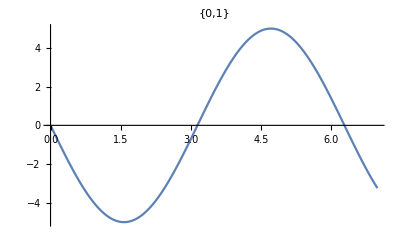
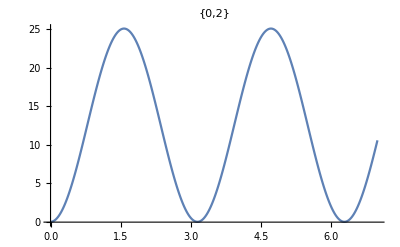
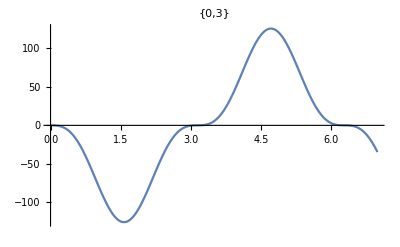
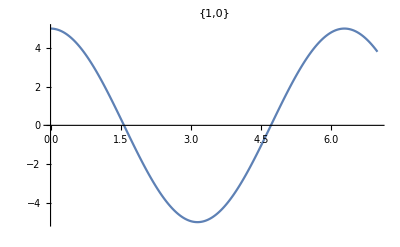
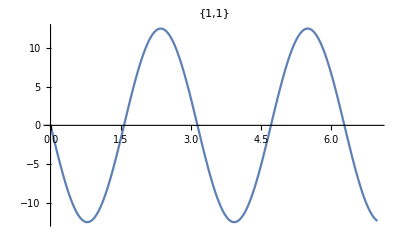
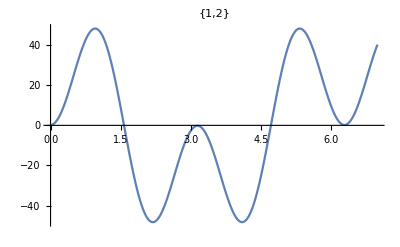
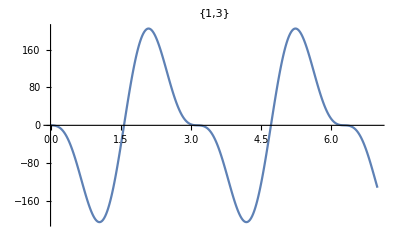
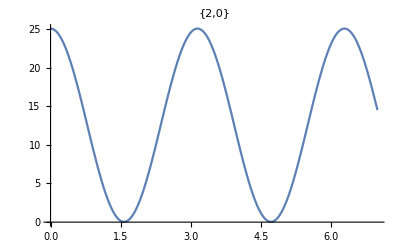

```mathematica
plots={};
Do[
If[Total[ks[[i]]]<10&&Total[ks[[i]]]>0,
AppendTo[plots,ListPlot[Thread[{ts,sol[[All,i]]}],Joined->True,PlotRange->All,PlotLabel->ks[[i]]]]
]
,{i,1,Length[moms]}]
plots
```

```mathematica
(* Verify with Monte Carlo *)
Ncases=10000;
cases=RandomVariate[BinormalDistribution[{μR,μRd},{σR,σRd},ρRRd],Ncases];
(*Nt=100;*)
β=2/Rey;
ω2= 2 γ Ca;
Clear[t];
myr=ParallelTable[
r[t]/.(NDSolve[
{r''[t] == -2 β r'[t]-ω2 r[t]-Cp,r[0]==cases[[i,1]],r'[0]==cases[[i,2]]},
r[t],
{t,0,T}]//First//First),
{i,1,Ncases}];
mydr=Table[
D[myr[[i]],t],{i,1,Ncases}];

(*ts2=Table[i,{i,0,T,T/Nt}];*)
ts2=myts;
Nt=Length[ts2];
P=Table[Table[{
myr[[j]]/.{t->ts2[[i]]},
mydr[[j]]/.{t->ts2[[i]]}},{j,1,Ncases}],
{i,1,Nt}];

nonlinmoments=Table[Table[{ts2[[i]],Moment[P[[i]],ks[[j,1;;2]]]},{i,1,Nt}],{j,1,Length[ks]}];

skewR=ParallelTable[{ts2[[i]],Skewness[P[[i]]][[1]]},{i,1,Nt}];
skewRd=ParallelTable[{ts2[[i]],Skewness[P[[i]]][[2]]},{i,1,Nt}];
kurtR=ParallelTable[{ts2[[i]],-3+Kurtosis[P[[i]]][[1]]},{i,1,Nt}];
kurtRd=ParallelTable[{ts2[[i]],-3+Kurtosis[P[[i]]][[2]]},{i,1,Nt}];
```

0.0200658

0.0198596

0.0155169

0.0155307

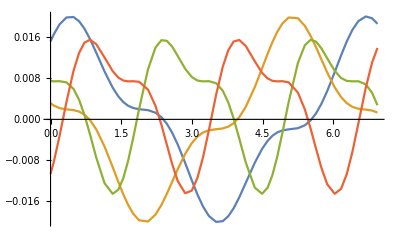

```mathematica
Max[skewR[[All,2]]]
Max[skewRd[[All,2]]]
Max[kurtR[[All,2]]]
Max[kurtRd[[All,2]]]
ListPlot[{skewR,skewRd,kurtR,kurtRd},Joined->True]
```

```mathematica
plts=ParallelTable[
Show[
DensityHistogram[P[[i]],PlotRange->{{xmin,xmax},{ymin,ymax},All}],
ListPlot[Flatten[myabscissa[[i]],1],PlotStyle->Red,PlotRange->{{xmin,xmax},{ymin,ymax}}]]
,{i,1,Length[P]}];
vid=ListAnimate[plts]
```

```mathematica
(*Export["~/Desktop/mov_3x2.avi",plts]*)
```